```mathematica
niters=5;
Xn=1;
Xnm1 =0.5;
F[x_]= 10 E^(x/2)Cos[2x]
solutions={};
For[i=1, i<= niters, i++,
Xnp1 = Xn - (Xn - Xnm1)/(F[Xn]-F[Xnm1])F[Xn];AppendTo[solutions , Xnp1];Print["iter= ",i," Xn= ", Xn, " Xnp1= ",Xnp1];
Xnm1 = Xn;
Xn = Xnp1;]
```

```mathematica
solutions//TableForm
```

0.751386
0.782726
0.785446
0.785398
0.785398

```mathematica
F[x_]= 10 E^(x/2)Cos[2x]
```

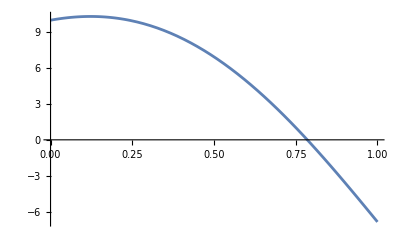

```mathematica
Plot[F[x],{x,0,1}]
```